```mathematica
EJ=2618.942;
EL=3EJ;
nmax=5;
nlistname=Table[(ToString[n])<>" JJs / Arm",{n,1,nmax}];
```

```mathematica
fϕm[i_,ϕ_]:=i/(i+1)(Mod[ϕ+π,2π]-π);
ϕm12[ϕ_]:=fϕm[1,ϕ];
ϕm23[ϕ_]:=fϕm[2,ϕ];
ϕm13[ϕ_]:=fϕm[1,ϕm23[ϕ]];
ϕm34[ϕ_]:=fϕm[3,ϕ];
ϕm24[ϕ_]:=fϕm[2,ϕm34[ϕ]];
ϕm14[ϕ_]:=fϕm[1,ϕm24[ϕ]];
ϕm45[ϕ_]:=fϕm[4,ϕ];
ϕm35[ϕ_]:=fϕm[3,ϕm45[ϕ]];
ϕm25[ϕ_]:=fϕm[2,ϕm35[ϕ]];
ϕm15[ϕ_]:=fϕm[1,ϕm25[ϕ]];
```

```mathematica
HJ1=-EJ(Cos[Subscript[φ, a]]+Cos[Subscript[φ, b]]+Cos[Subscript[φ, c]]+Cos[Subscript[φ, d]]-4);
HJ2=Plus@@(-2EJ(Cos[ϕm12[φ]]+Cos[φ-ϕm12[φ]]-2)/.{{φ->Subscript[φ, a]},{φ->Subscript[φ, b]},{φ->Subscript[φ, c]},{φ->Subscript[φ, d]}});
HJ3=Plus@@(-3EJ(Cos[ϕm13[φ]]+Cos[ϕm23[φ]-ϕm13[φ]]+Cos[φ-ϕm23[φ]]-3)/.{{φ->Subscript[φ, a]},{φ->Subscript[φ, b]},{φ->Subscript[φ, c]},{φ->Subscript[φ, d]}});
HJ4=Plus@@(-4EJ(Cos[ϕm14[φ]]+Cos[ϕm24[φ]-ϕm14[φ]]+Cos[ϕm34[φ]-ϕm24[φ]]+Cos[φ-ϕm34[φ]]-4)/.{{φ->Subscript[φ, a]},{φ->Subscript[φ, b]},{φ->Subscript[φ, c]},{φ->Subscript[φ, d]}});
HJ5=Plus@@(-5EJ(Cos[ϕm15[φ]]+Cos[ϕm25[φ]-ϕm15[φ]]+Cos[ϕm35[φ]-ϕm25[φ]]+Cos[ϕm45[φ]-ϕm35[φ]]+Cos[φ-ϕm45[φ]]-5)/.{{φ->Subscript[φ, a]},{φ->Subscript[φ, b]},{φ->Subscript[φ, c]},{φ->Subscript[φ, d]}});

Hshunt=EL/2(Subscript[φ, L1]^2+Subscript[φ, L2]^2+Subscript[φ, L3]^2+Subscript[φ, L4]^2);
({{Subscript[φ, a]}, {Subscript[φ, b]}, {Subscript[φ, c]}, {Subscript[φ, d]}})=({{1/2, 1/2, 1, 1/4}, {-1/2, 1/2, -1, 1/4}, {-1/2, -1/2, 1, 1/4}, {1/2, -1/2, -1, 1/4}}).({{Subscript[φ, x]}, {Subscript[φ, y]}, {Subscript[φ, z]}, {Subscript[φ, M]}});
solvecros=Flatten[Simplify[Solve[Subscript[φ, a]-Subscript[φ, L1]+Subscript[φ, L2]==Subscript[φ, ext]/4+2Pi Subscript[n, a]&&Subscript[φ, b]-Subscript[φ, L2]+Subscript[φ, L3]==Subscript[φ, ext]/4+2Pi Subscript[n, b]&&Subscript[φ, c]-Subscript[φ, L3]+Subscript[φ, L4]==Subscript[φ, ext]/4+2Pi Subscript[n, c]&&Subscript[φ, L1]+Subscript[φ, L2]+Subscript[φ, L3]+Subscript[φ, L4]==0,{Subscript[φ, L1],Subscript[φ, L2],Subscript[φ, L3],Subscript[φ, L4]}]/.Subscript[φ, M]->Subscript[φ, ext]+2Pi(Subscript[n, a]+Subscript[n, b]+Subscript[n, c]+Subscript[n, d])]/.{Subscript[n, a]->m,Subscript[n, b]->m,Subscript[n, c]->m,Subscript[n, d]->m}];
Hshunt=Simplify[Hshunt/.solvecros];
HJ1=Simplify[HJ1/.Subscript[φ, M]->Subscript[φ, ext]];
HJ2=Simplify[HJ2/.Subscript[φ, M]->Subscript[φ, ext]];
HJ3=Simplify[HJ3/.Subscript[φ, M]->Subscript[φ, ext]];
HJ4=Simplify[HJ4/.Subscript[φ, M]->Subscript[φ, ext]];
HJ5=Simplify[HJ5/.Subscript[φ, M]->Subscript[φ, ext]];

Htot1=Simplify[HJ1+Hshunt];
Htot2=Simplify[HJ2+Hshunt];
Htot3=Simplify[HJ3+Hshunt];
Htot4=Simplify[HJ4+Hshunt];
Htot5=Simplify[HJ5+Hshunt];
```

```mathematica
H1[ϕx_,ϕy_,ϕz_,ϕext_,EJ_,EL_]:=Htot1/.{Subscript[φ, x]->ϕx,Subscript[φ, y]-> ϕy,Subscript[φ, z]-> ϕz,Subscript[φ, ext]-> ϕext}
H2[ϕx_,ϕy_,ϕz_,ϕext_,EJ_,EL_]:=Htot2/.{Subscript[φ, x]->ϕx,Subscript[φ, y]-> ϕy,Subscript[φ, z]-> ϕz,Subscript[φ, ext]-> ϕext}
H3[ϕx_,ϕy_,ϕz_,ϕext_,EJ_,EL_]:=Htot3/.{Subscript[φ, x]->ϕx,Subscript[φ, y]-> ϕy,Subscript[φ, z]-> ϕz,Subscript[φ, ext]-> ϕext}
H4[ϕx_,ϕy_,ϕz_,ϕext_,EJ_,EL_]:=Htot4/.{Subscript[φ, x]->ϕx,Subscript[φ, y]-> ϕy,Subscript[φ, z]-> ϕz,Subscript[φ, ext]-> ϕext}
H5[ϕx_,ϕy_,ϕz_,ϕext_,EJ_,EL_]:=Htot5/.{Subscript[φ, x]->ϕx,Subscript[φ, y]-> ϕy,Subscript[φ, z]-> ϕz,Subscript[φ, ext]-> ϕext}

Hlist={H1,H2,H3,H4,H5};
H[ϕx_,ϕy_,ϕz_,ϕext_,n_,EJ_,EL_]:=Hlist[[n]][ϕx,ϕy,ϕz,ϕext,EJ,EL]
```

```mathematica
ip=Table[RandomReal[{-2π,2π},3],50];
ϕextlist=Join[Range[0,7, 0.7],Range[7.1,11, 0.1],Range[11.1,4π,0.4]];
Monitor[For[listEmin={};n=1,n≤nmax,n++,
Monitor[
t1=Table[
zt=Sort[Table[
res=Quiet[FindMinimum[H[ϕx,ϕy,ϕz,ϕext,n,EJ,EL],{ϕx,ip[[i,1]]},{ϕy,ip[[i,2]]},{ϕz,ip[[i,3]]}]];
{res[[1]],ϕx,ϕy,ϕz}/.res[[2]]
,{i,Length[ip]}]];
zt1={Flatten[{ϕext, zt[[1]]}]}
,{ϕext,ϕextlist}]
,ϕext];
listEmin=Insert[listEmin,t1,n]
],
n]
```

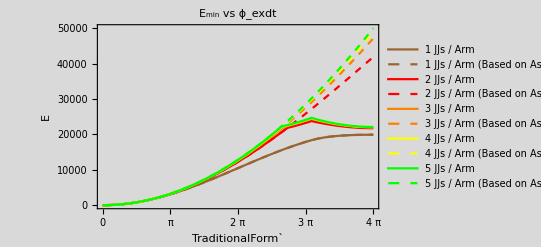

```mathematica
itpEmin[n_]:=Interpolation[listEmin[[n,All,1,{1,2}]]];

listEmin2=ToExpression[Import["listEmin based on Assumption.txt"]];
itpEmin2[n_]:=Interpolation[listEmin2[[n,All,1,{1,2}]]]
nlistname2=Flatten[Table[{nlistname[[n]],(ToString[n])<>" JJs / Arm (Based on Assumption)"},{n,1,nmax}]];

Plot[
Evaluate[Table[{itpEmin[n][x],itpEmin2[n][x]},{n,1,nmax}],{x,0,4π}], Frame->True, FrameLabel->{"TraditionalForm`","E"}, FrameTicks->{Automatic,{π Range[0,4,1/4],None}},PlotLegends->nlistname2,PlotStyle->{Brown,{Brown,Dashed},Red,{Red,Dashed},Orange,{Dashed,Orange},Yellow,{Yellow,Dashed},Green,{Green,Dashed}}, PlotLabel->Style["E_min vs ϕ_exdt",Bold, 16,Orange],GridLines->{π Range[0,4,1/4],Automatic},Background->LightGray]
```

```mathematica
ϕnode[n_,j_]:=Flatten[({{1/2, 1/2, 1, 1/4}, {-1/2, 1/2, -1, 1/4}, {-1/2, -1/2, 1, 1/4}, {1/2, -1/2, -1, 1/4}}).({{listEmin[[n,j,1,3]]}, {listEmin[[n,j,1,4]]}, {listEmin[[n,j,1,5]]}, {listEmin[[n,j,1,1]]}})]
ϕnode[2,Length[ϕextlist]]

ϕarm[n_,i_]:=Table[{ϕextlist[[j]],ϕnode[n,j][[If[i<4,i+1,1]]]-ϕnode[n,j][[i]]},{j,1,Length[listEmin[[n]]]}]
ϕarm[2,1][[Length[ϕextlist]]]
ϕm12[ϕarm[2,1][[Length[ϕextlist],2]]]
```

{4.80438,1.34562,4.80438,1.34562}

{12.3,-3.45876}

1.41221

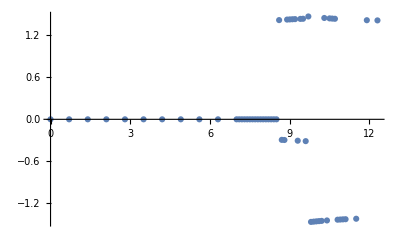

```mathematica
ListPlot[Table[{ϕextlist[[j]], ϕm12[ϕarm[2,1][[j,2]]]},{j,1,Length[ϕextlist]}],PlotRange->All]
```

```mathematica
ϕxmin[n_]:=Table[{listEmin[[n,k,1,1]],listEmin[[n,k,1,3]]},{k,1,Length[listEmin[[n]]]}]
ϕymin[n_]:=Table[{listEmin[[n,k,1,1]],listEmin[[n,k,1,4]]},{k,1,Length[listEmin[[n]]]}]
ϕzmin[n_]:=Table[{listEmin[[n,k,1,1]],listEmin[[n,k,1,5]]},{k,1,Length[listEmin[[n]]]}]

x2[n_]:=Monitor[Table[

{ϕextlist[[i]],1/2 D[H[ϕx,ϕy,ϕz,ϕextlist[[i]],n,EJ,EL],{ϕx,2}]/.{ϕx->ϕxmin[n][[i,2]],ϕy->ϕymin[n][[i,2]],ϕz->ϕzmin[n][[i,2]]}},{i,1,Length[ϕextlist]}],ϕextlist[[i]]]

xyz[n_]:=Monitor[Table[

{ϕextlist[[i]],D[H[ϕx,ϕy,ϕz,ϕextlist[[i]],n,EJ,EL],{ϕx,1},{ϕy,1},{ϕz,1}]/.{ϕx->ϕxmin[n][[i,2]],ϕy->ϕymin[n][[i,2]],ϕz->ϕzmin[n][[i,2]]}},{i,1,Length[ϕextlist]}],ϕextlist[[i]]]

x2z2[n_]:=Monitor[Table[

{ϕextlist[[i]],1/4 D[H[ϕx,ϕy,ϕz,ϕextlist[[i]],n,EJ,EL],{ϕx,2},{ϕz,2}]/.{ϕx->ϕxmin[n][[i,2]],ϕy->ϕymin[n][[i,2]],ϕz->ϕzmin[n][[i,2]]}},{i,1,Length[ϕextlist]}],ϕextlist[[i]]]

xyz3[n_]:=Monitor[Table[

{ϕextlist[[i]],1/6 D[H[ϕx,ϕy,ϕz,ϕextlist[[i]],n,EJ,EL],{ϕx,1},{ϕy,1},{ϕz,3}]/.{ϕx->ϕxmin[n][[i,2]],ϕy->ϕymin[n][[i,2]],ϕz->ϕzmin[n][[i,2]]}},{i,1,Length[ϕextlist]}],ϕextlist[[i]]]
```

```mathematica
x2list=Monitor[Table[x2[j],{j,1,nmax}],j];
```

```mathematica
xyzlist=Monitor[Table[xyz[j],{j,1,nmax}],j];
```

```mathematica
x2z2list=Monitor[Table[x2z2[j],{j,1,nmax}],j];
```

```mathematica
xyz3list=Monitor[Table[xyz3[j],{j,1,nmax}],j];
```

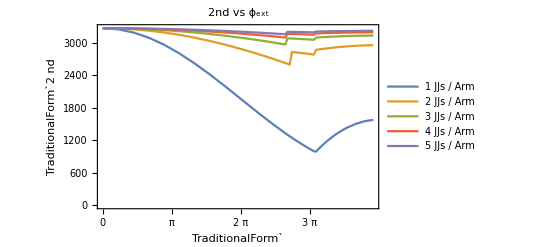

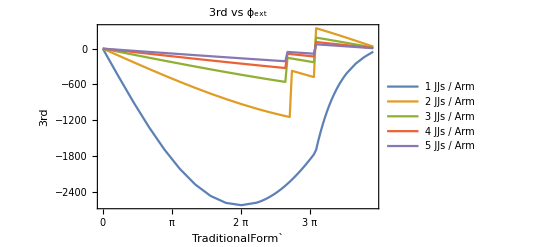

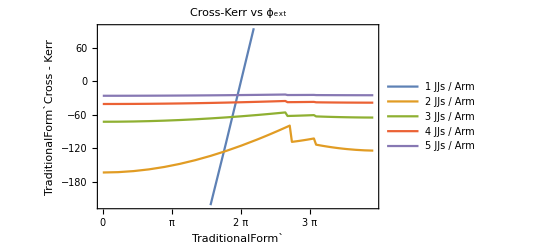

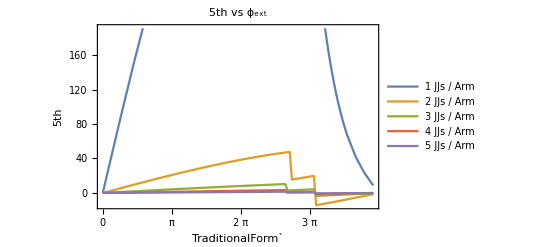

```mathematica
ListPlot[Table[x2list[[i]],{i,1,nmax}], Frame->True, FrameLabel->{"TraditionalForm`","TraditionalForm`2  nd"}, FrameTicks->{Automatic,{π Range[0,4,1/4],None}},PlotLegends->nlistname,PlotLabel->Style["2nd vs ϕ_ext",Bold, 16,Orange],Joined->True,PlotRange->All,GridLines->{π Range[0,4,1/2],Automatic}]

ListPlot[Table[xyzlist[[i]],{i,1,nmax}], Frame->True, FrameLabel->{"TraditionalForm`","3rd"}, FrameTicks->{Automatic,{π Range[0,4,1/4],None}},PlotLegends->nlistname,PlotLabel->Style["3rd vs ϕ_ext",Bold, 16,Orange],Joined->True,GridLines->{π Range[0,4,1/2],Automatic}]

ListPlot[Table[x2z2list[[i]],{i,1,nmax}], Frame->True, FrameLabel->{"TraditionalForm`","TraditionalForm`Cross - Kerr"}, FrameTicks->{Automatic,{π Range[0,4,1/4],None}},PlotLegends->nlistname,PlotLabel->Style["Cross-Kerr vs ϕ_ext",Bold, 16,Orange],Joined->True,GridLines->{π Range[0,4,1/2],Automatic}]

ListPlot[Table[xyz3list[[i]],{i,1,nmax}], Frame->True, FrameLabel->{"TraditionalForm`","5th"}, FrameTicks->{Automatic,{π Range[0,4,1/4],None}},PlotLegends->nlistname,PlotLabel->Style["5th vs ϕ_ext",Bold, 16,Orange],Joined->True,GridLines->{π Range[0,4,1/2],Automatic}]
```

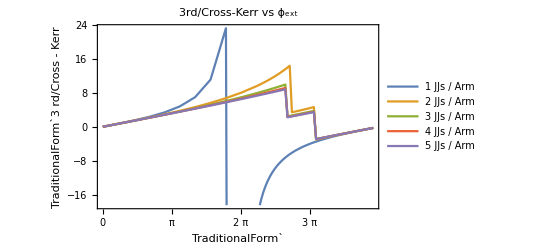

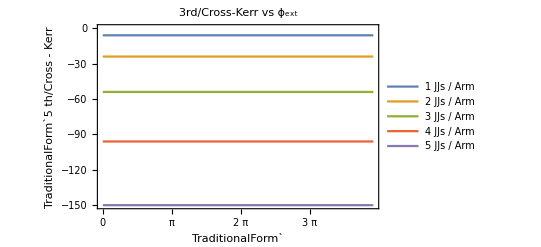

```mathematica
k3ratiolist[n_]:=Table[{ϕextlist[[i]],xyzlist[[n,i,2]]/x2z2list[[n,i,2]]},{i,1,Length[ϕextlist]}]
ListPlot[Table[k3ratiolist[i],{i,1,nmax}], Frame->True, FrameLabel->{"TraditionalForm`","TraditionalForm`3  rd/Cross - Kerr"}, FrameTicks->{Automatic,{π Range[0,4,1/4],None}},PlotLegends->nlistname,PlotLabel->Style["3rd/Cross-Kerr vs ϕ_ext",Bold, 16,Orange],Joined->True,GridLines->{π Range[0,4,1/2],Automatic}]

f3ratiolist[n_]:=Table[{ϕextlist[[i]],xyzlist[[n,i,2]]/xyz3list[[n,i,2]]},{i,1,Length[ϕextlist]}]
ListPlot[Table[f3ratiolist[i],{i,1,nmax}], Frame->True, FrameLabel->{"TraditionalForm`","TraditionalForm`5  th/Cross - Kerr"}, FrameTicks->{Automatic,{π Range[0,4,1/4],None}},PlotLegends->nlistname,PlotLabel->Style["3rd/Cross-Kerr vs ϕ_ext",Bold, 16,Orange],Joined->True,GridLines->{π Range[0,4,1/2],Automatic},PlotRange->All]
```

```mathematica
itpx2list=Table[Interpolation[x2list[[i]]],{i,1,nmax}];
itpxyzlist=Table[Interpolation[xyzlist[[i]]],{i,1,nmax}];
itpx2z2list=Table[Interpolation[x2z2list[[i]]],{i,1,nmax}];
```

```mathematica
Plot[Evaluate[Table[itpx2list[[i]][x],{i,1,nmax}]],{x,0,4π}]
pxyz=Plot[Evaluate[Table[itpxyzlist[[i]][x],{i,1,nmax}]],{x,0,4π}]
Plot[Evaluate[Table[itpx2z2list[[i]][x],{i,1,nmax}]],{x,0,4π}]
```